```mathematica
a = 3
```

3

```mathematica
Range[20]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20}

```mathematica
Table[x^2, {x, 10}]
```

{1,4,9,16,25,36,49,64,81,100}

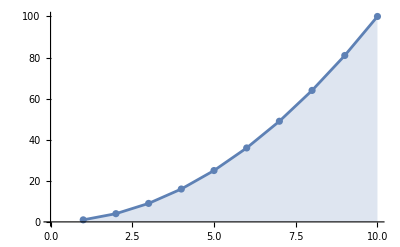

```mathematica
ListPlot[{1,4,9,16,25,36,49,64,81,100},Filling->Axis,Mesh->All,Joined->True]
```

```mathematica
?Table
```

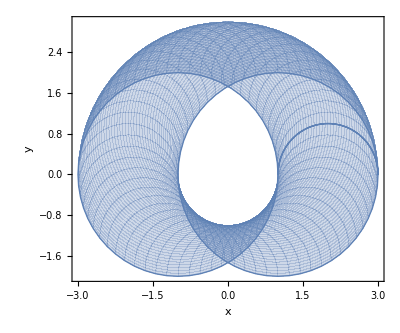

```mathematica
(* 参数函数图形的绘制，即图形的横坐标与纵坐标也是函数 *)
ParametricPlot[{Cos[θ]+2 Cos[ϕ],Sin[θ]+2 Sin[ϕ]},{θ,0,π},{ϕ,0,2 π},AxesLabel->{"x","y"}]
```

```mathematica
Manipulate[Graphics[{Circle[{Cos[θ],Sin[θ]},2]},Axes->True,PlotRange->{{-3,3},{-3,3}},AxesLabel->{"x","y"}],{θ,0,π}]
```

```mathematica
staticPlot=ParametricPlot[{Cos[θ]+2 Cos[ϕ],Sin[θ]+2 Sin[ϕ]},{θ,0,π},{ϕ,0,2 π},PlotStyle->Blue,AxesLabel->{"x","y"},PlotRange->{{-3,3},{-3,3}},Axes->True];

Manipulate[Column[{Row[{"当前 θ 值：",Row[{TraditionalForm[Rationalize[θ/π]]," π"}," "]}],Show[staticPlot,Graphics[{Red,Thick,Circle[{Cos[θ],Sin[θ]},2]}],PlotRange->{{-3,3},{-3,3}},AxesLabel->{"x","y"}, ImageSize->600]}],{{θ,0,"θ"},0,π}]
```

```mathematica
{}
```